# Dynamical Analysis of Referential Communication

## Thomas Gaul

## Initialization

```mathematica
Get["Dynamica`"];
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
(* if CTRNN5y takes too long to define, edit Dynamica.m and lower the
$DynamicaSymbolicThreshold (the default is 5). Use this line to verify. *)
$DynamicaSymbolicThreshold
```

4

### Definitions for Loading Phenotype

```mathematica
$ParentDirectory = FileNameJoin[{NotebookDirectory[],"..","EvoP2"}];
SetDirectory[$ParentDirectory];
fileName[pop_]:=FileNameJoin[{StringJoin["Pop-",ToString[pop]],"phenotype.dat"}];
SetPhenotype[pop_]:=Module[{data,taus,thetas,weights,sensorweights},data=Flatten[Import[fileName[pop],"Table"]];
taus=data[[1;;5]];
thetas=data[[6;;10]];
weights=Partition[data[[11;;35]],5];
sensorweights=data[[36;;]];
CTRNN5y/.{
τ1->taus[[1]],τ2->taus[[2]],τ3->taus[[3]],τ4->taus[[4]],τ5->taus[[5]],
θ1->thetas[[1]],θ2->thetas[[2]],θ3->thetas[[3]],θ4->thetas[[4]],θ5->thetas[[5]],
w11->weights[[1,1]],w21->weights[[2,1]],w31->weights[[3,1]],w41->weights[[4,1]],w51->weights[[5,1]],
w12->weights[[1,2]],w22->weights[[2,2]],w32->weights[[3,2]],w42->weights[[4,2]],w52->weights[[5,2]],
w13->weights[[1,3]],w23->weights[[2,3]],w33->weights[[3,3]],w43->weights[[4,3]],w53->weights[[5,3]],
w14->weights[[1,4]],w24->weights[[2,4]],w34->weights[[3,4]],w44->weights[[4,4]],w54->weights[[5,4]],
w15->weights[[1,5]],w25->weights[[2,5]],w35->weights[[3,5]],w45->weights[[4,5]],w55->weights[[5,5]],
sw1->sensorweights[[1]],sw2->sensorweights[[2]],sw3->sensorweights[[3]],sw4->sensorweights[[4]],sw5->sensorweights[[5]]
}
];
```

### Dynamical System Definition

```mathematica
σ[x_]:=1/(1+ⅇ^-x);
```

```mathematica
CTRNN5y=DynamicalSystem[
{
(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w31 σ[y3+θ3]+w41 σ[y4+θ4]+w51 σ[y5+θ5]+sw1 d)/τ1,
(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w32 σ[y3+θ3]+w42 σ[y4+θ4]+w52 σ[y5+θ5]+sw2 d)/τ2,
(-y3+w13 σ[y1+θ1]+w23 σ[y2+θ2]+w33 σ[y3+θ3]+w43 σ[y4+θ4]+w53 σ[y5+θ5]+sw3 d)/τ3,
(-y4+w14 σ[y1+θ1]+w24 σ[y2+θ2]+w34 σ[y3+θ3]+w44 σ[y4+θ4]+w54 σ[y5+θ5]+sw4 d)/τ4,
(-y5+w15 σ[y1+θ1]+w25 σ[y2+θ2]+w35 σ[y3+θ3]+w45 σ[y4+θ4]+w55 σ[y5+θ5]+sw5 d)/τ5
},
{{y1,-35,35},{y2,-35,35},{y3,-35,35},{y4,-35,35},{y5,-35,35}},
{
{θ1,-16,16},{θ2,-16,16},{θ3,-16,16},{θ4,-16,16},{θ5,-16,16},
{τ1,1,30},{τ2,1,30},{τ3,1,30},{τ4,1,30},{τ5,1,30},
{sw1,-16,16},{sw2,-16,16},{sw3,-16,16},{sw4,-16,16},{sw5,-16,16},
{w11,-16,16},{w21,-16,16},{w31,-16,16},{w41,-16,16},{w51,-16,16},
{w12,-16,16},{w22,-16,16},{w32,-16,16},{w42,-16,16},{w52,-16,16},
{w13,-16,16},{w23,-16,16},{w33,-16,16},{w43,-16,16},{w53,-16,16},
{w14,-16,16},{w24,-16,16},{w34,-16,16},{w44,-16,16},{w54,-16,16},
{w15,-16,16},{w25,-16,16},{w35,-16,16},{w45,-16,16},{w55,-16,16},
{d,0,1}
}
];
```

### Definitions for Activation States

```mathematica
val[agent_,param_]:=DSParameterValue[agent,param]
out[agent_,yys_]:={σ[yys[[1]]+val[agent,θ1]],σ[yys[[2]]+val[agent,θ2]],σ[yys[[3]]+val[agent,θ3]],σ[yys[[4]]+val[agent,θ4]],σ[yys[[5]]+val[agent,θ5]]}
```

### Loading Agent Phenotype

```mathematica
A = SetPhenotype[1]; (* using agent 1 for dynamical analysis *)
```

## Bifurcation Analysis Functions

### Bifurcation Data Functions

```mathematica
BData[sys_,λ_,λmin_,λmax_,λstep_]:=Module[{SNodes={},SPlot={},uSNodes={},uSPlot={},Saddles={},SaddlePlot={},nonH={},nonHPlot={},currEPs,λs,idx},
For[i=λmin,i<=λmax,i+=λstep,
currEPs=EquilibriumPoints[sys/.{λ->i},Tries->500];
SNodes=Cases[currEPs,ep_/;ep[[4]]===Stable];
uSNodes=Cases[currEPs,ep_/;ep[[4]]===Unstable];
Saddles=Cases[currEPs,ep_/;ep[[4]]===Saddle];
nonH=Cases[currEPs,ep_/;ep[[4]]===Nonhyperbolic];
SPlot=Join[SPlot,Table[Join[{i},SNodes[[j,3]]],{j,Length[SNodes]}]];
uSPlot=Join[uSPlot,Table[Join[{i},uSNodes[[j,3]]],{j,Length[uSNodes]}]];
SaddlePlot=Join[SaddlePlot,Table[Join[{i},Saddles[[j,3]]],{j,Length[Saddles]}]];
nonHPlot=Join[nonHPlot,Table[Join[{i},nonH[[j,3]]],{j,Length[nonH]}]];
];
{SPlot,uSPlot,SaddlePlot,nonHPlot}
];
```

```mathematica
(* function must apply to list and return list *)
TransformBData[func_,data_]:=Module[{S,uS,Saddles,nonH},
S=data[[1]];uS=data[[2]];Saddles=data[[3]];nonH=data[[4]];
S=Join[{#[[1]]},func@@{#[[2;;]]}]&/@S;
uS=Join[{#[[1]]},func@@{#[[2;;]]}]&/@uS;
Saddles=Join[{#[[1]]},func@@{#[[2;;]]}]&/@Saddles;
nonH=Join[{#[[1]]},func@@{#[[2;;]]}]&/@nonH;
{S,uS,Saddles,nonH}
];
```

### Bifurcation Plotting Functions

```mathematica
PlotBifurcationDiagram[sys_,λ_,λmin_,λmax_,λstep_,vars_]:=PlotBifurcationDiagram[BData[sys,λ,λmin,λmax,λstep],sys,vars];
```

```mathematica
PlotBifurcationDiagram[data_,sys_,vars_]:=Module[{idx,dim,SPlot,uSPlot,SaddlePlot,nonHPlot},
idx=Flatten[Position[sys[[3]],x_/;MemberQ[vars,x]]]+1;
SPlot=#[[Join[{1},idx]]]&/@data[[1]];
uSPlot=#[[Join[{1},idx]]]&/@data[[2]];
SaddlePlot=#[[Join[{1},idx]]]&/@data[[3]];
nonHPlot=#[[Join[{1},idx]]]&/@data[[4]];
dim=Length[SPlot[[1]]]-1;
Which[
dim==1,Show[
ListPlot[SPlot,PlotStyle->Blue,PlotRange->All,Axes->True],
ListPlot[uSPlot,PlotStyle->Red,PlotRange->All,Axes->True],
ListPlot[SaddlePlot,PlotStyle->Green,PlotRange->All,Axes->True],
ListPlot[nonHPlot,PlotStyle->Black,PlotRange->All,Axes->True],
ImageSize->Large
],
dim==2,Show[
ListPointPlot3D[SPlot,PlotStyle->{Blue,Tiny},PlotRange->All],
ListPointPlot3D[uSPlot,PlotStyle->{Red,Tiny},PlotRange->All],
ListPointPlot3D[SaddlePlot,PlotStyle->{Green,Tiny},PlotRange->All],
ListPointPlot3D[nonHPlot,PlotStyle->{Black,Tiny},PlotRange->All],
ImageSize->Large
]
]
];
```

## Phase Plane Analysis

### Time Scale With No Sensor Activation

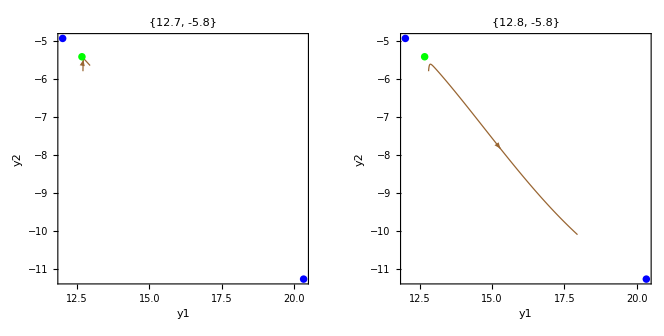

```mathematica
GraphicsRow[{
Show[
DisplayPhasePortrait[A/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->All,EquilibriumPointStyle->{PointSize[0.03]}],
DisplayTrajectories[A/.{d->0},{{12.7,-5.8,-1.0222608056533848,29.599883008269867,-2.789352727820398}},200,StateVariables->{y1,y2},PlotRange->All,PlotPoints->250,PlotStyle->{Thickness[.005],Brown}],
ImageSize->Small,PlotLabel->"{12.7, -5.8}"
],
Show[
DisplayPhasePortrait[A/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->All,EquilibriumPointStyle->{PointSize[0.03]}],
DisplayTrajectories[A/.{d->0},{{12.8,-5.8,-1.0222608056533848,29.599883008269867,-2.789352727820398}},200,StateVariables->{y1,y2},PlotRange->All,PlotPoints->250,PlotStyle->{Thickness[.005],Brown}],
ImageSize->Small,PlotLabel->"{12.8, -5.8}"
]
}]
```

```mathematica
Print["y1 Time Constant: ",A[[9,-5]]]
Print["y2 Time Constant: ",A[[9,-4]]]
Print["y3 Time Constant: ",A[[9,-3]]]
Print["y4 Time Constant: ",A[[9,-2]]]
Print["y5 Time Constant: ",A[[9,-1]]]
```

y1 Time Constant: τ1→29.98083099999999845408638066147

y2 Time Constant: τ2→16.65731604999999859728632145561

y3 Time Constant: τ3→2.053627999999999786950866109692

y4 Time Constant: τ4→29.96783899999999789542926009744

y5 Time Constant: τ5→6.260788500000000311729309032671

```mathematica
eps=EquilibriumPoints[A/.{d->0}]
```

{EquilibriumPoint[Stable,Node,{11.9971,-4.93765,-1.02226,29.5999,-2.78935}],EquilibriumPoint[Saddle,Node,{12.6648,-5.41964,-2.00339,29.0862,-2.60136}],EquilibriumPoint[Stable,Node,{20.3372,-11.2645,-13.5685,22.7658,-0.442715}]}

```mathematica
SaddlePoint=eps[[2,3]]
```

{12.6648,-5.41964,-2.00339,29.0862,-2.60136}

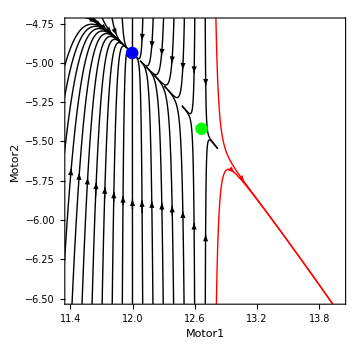

```mathematica
flow=Flatten[Table[Join[{12+i,-4.9-j},SaddlePoint[[3;;]]],{i,-1,.7,.1},{j,-.2,2,2.1}],1];
window={{11.4,14},{-6.5,-4.75}};
fig12=Show[
DisplayTrajectories[A/.{d->0},flow,150,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->Black,FrameLabel->{"Motor1","Motor2"}],
DisplayTrajectories[A/.{d->0},{Join[{12.8,-4.6},SaddlePoint[[3;;]]],Join[{12.8,-6.9},SaddlePoint[[3;;]]]},150,StateVariables->{y1,y2},PlotRange->window,Arrows->1,PlotStyle->Red],
DisplayPhasePortrait[A/.{d->0},StateVariables->{y1,y2},Tries->100,PlotRange->window,
SaddleManifolds->False,SaddleManifoldDuration->1500,SaddleManifoldPlotPoints->250,SaddleManifoldStyle->Thick],
ImageSize->Medium,PlotLabel->""
]
```

```mathematica
Export["../Plots/Gaul.fig12.pdf",fig12]
```

../Plots/Gaul.fig12.pdf

```mathematica
(* saddle point in activation space *)
out[A,SaddlePoint]
```

{0.160467,0.999943,1.5597×10^-8,1.,1.10228×10^-6}

### Looking for Basins of Attraction

```mathematica
flow=Flatten[Table[Join[{i,j},SaddlePoint[[3;;]]],{i,5,30,2},{j,-25,0,2.5}],1];
Length[flow]
```

143

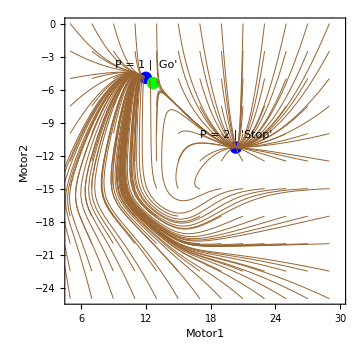

```mathematica
window={{5,30},{-25,0}};
Show[
DisplayPhasePortrait[A/.{d->0},PlotRange->window,StateVariables->{y1,y2},Tries->100,FrameLabel->{"Motor1","Motor2"}],
DisplayTrajectories[A/.{d->0},flow,200,PlotRange->window,StateVariables->{y1,y2},Arrows->0],
Graphics[Text[Framed[Style["P = 1 | 'Go'",Blue,Italic,12,FontFamily->"Times"],
FrameMargins->1,Background->White,FrameStyle->Blue],
eps[[1,3,{1,2}]]+{0,1.2}]],
Graphics[Text[Framed[Style["P = 2 | 'Stop'",Blue,Italic,12,FontFamily->"Times"],
FrameMargins->1,Background->White,FrameStyle->Blue],
eps[[3,3,{1,2}]]+{0,1.2}]],
ImageSize->Medium
]
```

```mathematica
Export["../Plots/DA-0-phaseprotrait.jpeg",%]
```

../Plots/DA-0-phaseprotrait.jpeg

### Phase Space by Contact Sensor

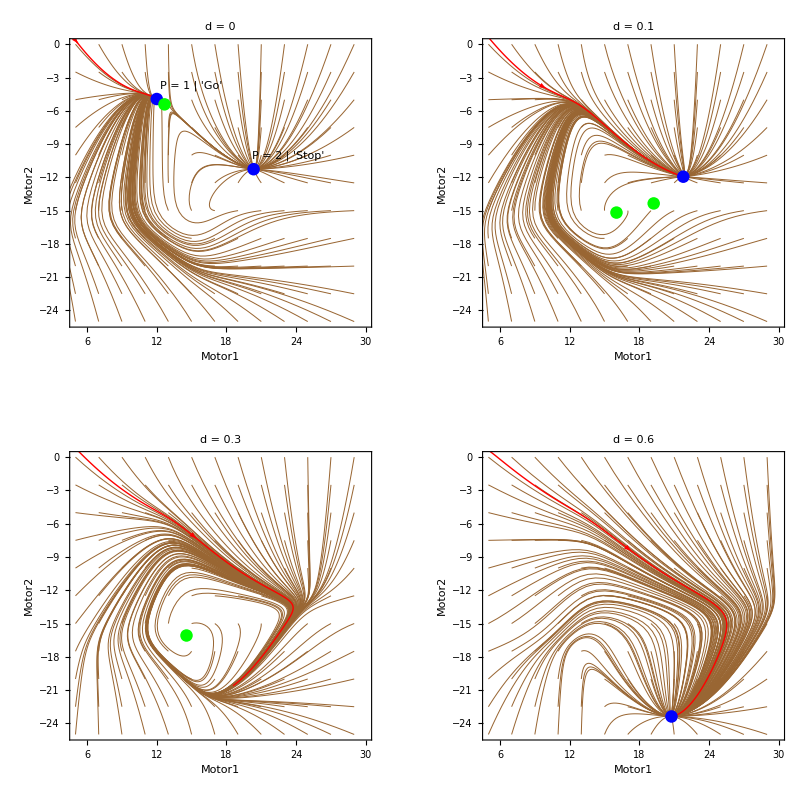

```mathematica
flow=Flatten[Table[Join[{i,j},SaddlePoint[[3;;]]],{i,5,30,2},{j,-25,0,2.5}],1];
window={{5,30},{-25,0}};
With[{u=0,v=.1,w=.3,l=.6},
fig11=GraphicsGrid[{{
Show[
DisplayTrajectories[A/.{d->u},flow,200,PlotRange->window,StateVariables->{y1,y2},Arrows->0,FrameLabel->{"Motor1","Motor2"}],
DisplayTrajectories[A/.{d->u},{{0,0,0,0,0}},200,PlotRange->window,StateVariables->{y1,y2},Arrows->1,PlotStyle->Red,PlotPoints->200],
DisplayPhasePortrait[A/.{d->u},PlotRange->window,StateVariables->{y1,y2},Tries->300],
Graphics[Text[Framed[Style["P = 1 | 'Go'",Blue,Italic,10,FontFamily->"Times"],
FrameMargins->1,Background->White,FrameStyle->Blue],
eps[[1,3,{1,2}]]+{3,1.2}]],
Graphics[Text[Framed[Style["P = 2 | 'Stop'",Blue,Italic,10,FontFamily->"Times"],
FrameMargins->1,Background->White,FrameStyle->Blue],
eps[[3,3,{1,2}]]+{3,1.2}]],
ImageSize->Medium,PlotLabel->StringJoin["d = ",ToString[u]]
],
Show[
DisplayTrajectories[A/.{d->v},flow,200,PlotRange->window,StateVariables->{y1,y2},Arrows->0,FrameLabel->{"Motor1","Motor2"}],
DisplayTrajectories[A/.{d->v},{{0,0,0,0,0}},200,PlotRange->window,StateVariables->{y1,y2},Arrows->1,PlotStyle->Red,PlotPoints->200],
DisplayPhasePortrait[A/.{d->v},PlotRange->window,StateVariables->{y1,y2},Tries->300],
ImageSize->Medium,PlotLabel->StringJoin["d = ",ToString[v]]
]},{
Show[
DisplayTrajectories[A/.{d->w},flow,200,PlotRange->window,StateVariables->{y1,y2},Arrows->0,FrameLabel->{"Motor1","Motor2"}],
DisplayTrajectories[A/.{d->w},{{0,0,0,0,0}},200,PlotRange->window,StateVariables->{y1,y2},Arrows->1,PlotStyle->Red,PlotPoints->200],
DisplayPhasePortrait[A/.{d->w},PlotRange->window,StateVariables->{y1,y2},Tries->500],
ImageSize->Medium,PlotLabel->StringJoin["d = ",ToString[w]]
],
Show[
DisplayTrajectories[A/.{d->l},flow,200,PlotRange->window,StateVariables->{y1,y2},Arrows->0,FrameLabel->{"Motor1","Motor2"}],
DisplayTrajectories[A/.{d->l},{{0,0,0,0,0}},200,PlotRange->window,StateVariables->{y1,y2},Arrows->1,PlotStyle->Red,PlotPoints->200],
DisplayPhasePortrait[A/.{d->l},PlotRange->window,StateVariables->{y1,y2},Tries->300],
ImageSize->Medium,PlotLabel->StringJoin["d = ",ToString[l]]
]
}
}]
]
```

```mathematica
Export["../Plots/Gaul.fig11.pdf",fig11]
```

../Plots/Gaul.fig11.pdf

### Nodes in Activation Space

```mathematica
(* activation space has values too extreme to accuractely analyse in full *)
```

```mathematica
EquilibriumPoints[A/.{d->0}]
```

{EquilibriumPoint[Stable,Node,{11.9971,-4.93765,-1.02226,29.5999,-2.78935}],EquilibriumPoint[Saddle,Node,{12.6648,-5.41964,-2.00339,29.0862,-2.60136}],EquilibriumPoint[Stable,Node,{20.3372,-11.2645,-13.5685,22.7658,-0.442715}]}

```mathematica
Stable1={11.99712610394856,-4.937650936282833,-1.0222608056533806,29.599883008269874,-2.7893527278203987};
Stable2={20.337155162659986,-11.264540886436732,-13.568487897552082,22.765773088231597,-0.4427154571108858};
Print["'go' attractor: ",out[Stable1]]
Print["'stop' attractor: ",out[Stable2]]
```

'go' attractor: out[{11.9971,-4.93765,-1.02226,29.5999,-2.78935}]

'stop' attractor: out[{20.3372,-11.2645,-13.5685,22.7658,-0.442715}]

## Bifurcation Analysis

```mathematica
(* takes forever to evaluate -- importing recommended *)
data=BData[A,d,0,1,.01];
```

```mathematica
Export["../Dynamical-Analysis/BifurcationData.mx",data];
```

```mathematica
data=Import["../Dynamical-Analysis/BifurcationData.mx"];
```

```mathematica
(* finding missed points *)
EquilibriumPoints[A/.{d->.507},Tries->500]
```

{EquilibriumPoint[Saddle,Mixed,{13.6712,-17.8721,-11.1586,20.5466,-6.2343}],EquilibriumPoint[Saddle,Node,{13.9013,-18.504,-11.939,19.7347,-6.17172}],EquilibriumPoint[Stable,Node,{19.1596,-22.854,-20.1923,14.9328,-4.69363}]}

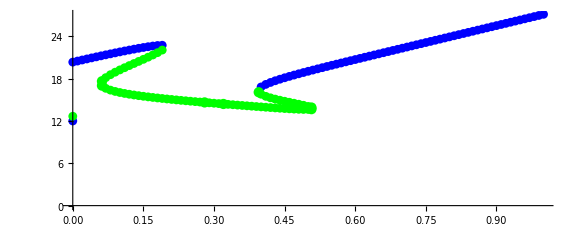

```mathematica
missed={{.062,17.005391789064376},{.062,17.627933914320938},{.28,14.624659893654236},{.32,14.405588198880139},{.395,16.069084973951743},{.507,13.671170383792893},{.507,13.901342197392657}};
Show[
PlotBifurcationDiagram[data,A,{y1}],
ListPlot[missed,PlotStyle->Green,Axes->True],
AspectRatio->.4,ImageSize->Large
]
```

```mathematica
Export["../Plots/DA-bifurcation.jpeg",%]
```

../Plots/DA-bifurcation.jpeg

```mathematica
func[x_]:=Table[σ[x[[i]]+A[[6,i]]/.A[[9]]],{i,Length[x]}];
func2[x_]:=Table[{x[[i,1]],σ[x[[i,j+1]]+A[[6,j]]/.A[[9]]]},{j,Length[x[[1]]]-1},{i,Length[x]}];
odata=TransformBData[func,data];
omissed=func2[missed];
```

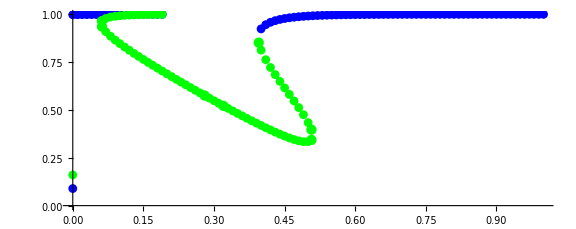

```mathematica
Show[
PlotBifurcationDiagram[odata,A,{y1}],
ListPlot[omissed,PlotStyle->Green],
AspectRatio->.4,ImageSize->Large
]
```

```mathematica
Export["../Plots/DA-output-bifurcation.jpeg",%]
```

../Plots/DA-output-bifurcation.jpeg